# 18: Least Squares Conditioning

## Matrix Condition Number for A∈ℝ^(m×m)

The matrix condition number is κ(A)=σ_1/σ_m.

κ(A) is the condition number for A.x=b→x  and A.x.

Not all problems involving a matrix A have this condition number!

## Least Squares Problem

The least squares problem for A∈ℝ^(m×n) and b∈ℝ^m with m>n is 
	x=armin_w||A.w-b(||)^2 and y=A.x is also of interest. 
We have seen several algorithms for this problem: QR, Normal Equations aka Projective, and SVD.  Every software package has a built in black-box command.

The simplest way to write the solution is x=A^+.b and y=P.b where A^+ is the pseudo inverse and P=A.A^+is the orthogonal projector onto the range of A.  Just a reminder, When a TS A is full rank we have
	A^+=(Aᵀ.A)^-1.Aᵀ  and P=A.A^+=A.(Aᵀ.A)^-1.Aᵀ
Note, P is symmetric and a projector i.e. P.P=P.

```mathematica
{m,n}={12,4};
A=RandomReal[{-1,1},{m,n}]; b=RandomReal[{-1,1},m];
x=LeastSquares[A,b];
{u1,u2}=Orthogonalize[RandomReal[{-1,1},{2,n}]];
res[ϵ1_,ϵ2_]:= Norm[A.(x+ϵ1 u1 + ϵ2 u2)-b]^2
TabView[{
"3D"->Plot3D[ res[ϵ1,ϵ2],{ϵ1,-1,1},{ϵ2,-2,2},
PlotLegends->Automatic],
"Contours"->ContourPlot[ res[ϵ1,ϵ2],{ϵ1,-1,1},{ϵ2,-2,2},
PlotLegends->Automatic,
Epilog->{Red, Point[{0,0}]}]}]
```

12

#### Assumptions and Definitions

Assume that A is full rank so that κ(A)=σ_1/σ_m is finite!

Write θ=ArcCos[||y||/||b||]=ArcCos[||P.b||/||b||]

Write η=||A||||x||/||y||=||A||||x||/||A.x||

## Everything is “diagonal”

Big picture: Remember everything is diagonal if we look at it correctly since 
	A=U.S.Vᵀ
and we are going to use the rotation invariant 2-norms and induced two norms.

The least squares problem for A=U.S.Vᵀ∈ℝ^(m×n) and b∈ℝ^m with m>n is 
	x=argmin_w||U.S.(Vᵀ.w)-b(||)^2 and y=U.S.Vᵀ.w
or equivalently if we put v=Vᵀ.w  i.e. w=V.v
	z^*=argmin_z||S.z-Uᵀ.b(||)^2
	x=V.z^*and y=U.S.z^*

Diagonal problems are easy.  Write Uᵀ.b=[b_1;b_2] and S=[S_1; 0] then
	z^*=argmin_z||S.z-Uᵀ.b(||)^2
is the same as 
	z^*=argmin_z||S_1.z-b_1(||)^2+||0-b_2(||)^2 =argmin_z||S_1.z-b_1(||)^2  
The answer is simply 
	z^*=S_1^-1.b_1=(S_1^-1| 0).(b_1
b_2)
The pseudo inverse of the diagonal problem is (S_1^-1| 0) and the projector of the diagonal problem is P=(I | 0
0 | 0).

The book does the conditioning computation geometrically by making everything diagonal.

We are going to do the computation more analytically.

## Derivatives of P and A^+

Assume that A(t) is a smooth vector valued function satisfying A(0)=(S_1
0) and A'(0)=(dA_1
dA_2) .  This defines vector valued functions 
	F(t)=(Aᵀ(t).A(t))^-1.Aᵀ(t)  and P(t)=A(t).F(t)
We want to compute P'(0) and F'(0) so that we can use the “derivative” formulas for the condition numbers.

#### P'(0)

This is not as tricky or weird as it looks.  We are going to write 
	P(t)=(P_11(t) | P_12(t)
P_21(t) | P_22(t)), note that P(0)=(I_n | 0
0 | 0), and write P'(0)=(dP_11 | dP_12
dP_21 | dP_22). 
We can work out P'(0) using the properties
	P.A=A, P=Pᵀ, and P.P=P.

Since P(t)=P(t)ᵀ we have P'(t)=P'(t)ᵀ  and evaluating at zero gives dP_21=(dP_12)ᵀ.

Since P(t).P(t)=P(t) we have P'(t).P(t)+P(t).P'(t)=P'(t) . Evaluating at zero gives
	(dP_11 | dP_12
dP_21 | dP_22).(I_n | 0
0 | 0)+(I_n | 0
0 | 0).(dP_11 | dP_12
dP_21 | dP_22)=(dP_11 | dP_12
dP_21 | dP_22)
which is simply 
	(2 dP_11 | dP_12
dP_21 | 0)=(dP_11 | dP_12
dP_21 | dP_22)
which means dP_11=dP_22=0.

Since P(t).A(t)=A(t) we have P'(t).A(t)+P(t).A'(t)=A'(t) . Evaluating at zero gives
	(0 | dP_12
dP_21 | 0).(S_1
0)+(I_n | 0
0 | 0).(dA_1
dA_2)=(dA_1
dA_2)
which is simply
	(0
dP_21.S_1)+(dA_1
0)=(dA_1
dA_2) or dP_21=dA_2.S_1^-1.
Putting it all together we have
	P'(0)=(0 | (dA_2.S_1^-1)ᵀ
dA_2.S_1^-1 | 0).

I suspect some of you think this is to good to be true. Lets check the formula

```mathematica
Clear[M,P]
{m,n}={12,3};
(* Define a test problem.  First the pertrurbed matrix *)
A=ConstantArray[0,{m,n}];
σs=Reverse[Sort[RandomReal[{0.1,10},n]]];
S1=DiagonalMatrix[σs];A⟦1;;n,1;;n⟧=S1;
(* Now the derivative *)
dA=RandomReal[{-1,1},{m,n}];dA1=dA⟦1;;n,1;;n⟧;dA2=dA⟦n+1;;m,1;;n⟧;
(* Building the functions *)
M[t_]:=A + dA t
P[t_]:=M[t].PseudoInverse[M[t]]
(* Evaluating a Finite Difference approximation*)
ϵ=1.0*10^-4;FD=(P[ϵ]-P[-ϵ])/(2ϵ);
(* Construct analytical expression *)
dP21=dA2.Inverse[S1];
dP = ArrayFlatten[({{0, dP21ᵀ}, {dP21, 0}})];
(* Compute norm of difference *)
Norm[dP-FD]
```

5.22251×10^-10

This all checks out.  We are going to use this formula to work out the derivative of the pseudoinverse (A(t))^+.

#### F'(0) where F(t) =(A(t))^+

We write F'(0)=(dF_1 | | | dF_2) and remember that
	F(t).A(t)=I_n
Differentiating and evaluating at zero gives
	(dF_1 | | | dF_2).(S_1
0)+(S_1^-1 | | | 0).(dA_1
dA_2)=(0)
or in other words dF_1.S_1=-S_1^-1.dA_1so 
	dF_1=-S_1^-1.dA_1.S_1^-1
We still need to find the last piece dF_2.

using P'(0), F(0), and A(0) and the identity 
	P(t).F(t)ᵀ=F(t)ᵀ.
Differentiating gives
	P'(t).F(t)ᵀ+ P(t).(F'(t))ᵀ=(F'(t))ᵀ
and evaluating at zero gives
	P'(0).(F(0))ᵀ+P(0).(F'(0))ᵀ=(F'(0))ᵀ.
Plugging in all the bits we know and writing F'(0)=(dF_1 | dF_2) we get
	(0 | (dA_2.S_1^-1)ᵀ
dA_2.S_1^-1 | 0).(S_1^-1
0)+(I_n | 0
0 | 0).((dF_1)ᵀ
(dF_2)ᵀ) =((dF_1)ᵀ
dF_2) 
Expanding out we get
	(0
dA_2)+(dF_1
0)=(dF_1
dF_2)
Matching up the pieces we get information from the lower block
	dF_2=dA_2
The upper block contains no information.
	dF_1=dF_1.
We still

```mathematica
{m,n}={12,3};
A=RandomReal[{-1,1},{m,n}];
APinv=PseudoInverse[A];
APinv.A
```

{{1.,4.05925×10^-16,-1.38778×10^-17},{1.11022×10^-16,1.,-2.5327×10^-16},{2.77556×10^-17,-2.34188×10^-16,1.}}

{{0,0,1.14114×10^-10,6.16712,-2.95567,-2.65803,7.56705,3.76413,7.36188,-7.40168,2.49949,7.47929},{0,0,0,3.29381,-1.6205,4.33196,1.00966,1.63861,-1.03772,-2.36705,-3.57098,1.64501},{1.44372×10^-10,0,3.34601×10^-10,-0.58254,-1.17244,1.16168,-1.08492,0.657424,2.28383,-2.20001,-0.0758617,-2.25645}}

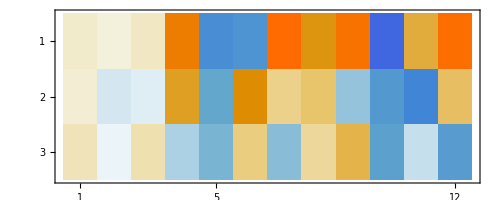

```mathematica
Clear[M,P]
{m,n}={12,3};
(* Define a test problem.  First the pertrurbed matrix *)
A=ConstantArray[0,{m,n}];
σs=Reverse[Sort[RandomReal[{0.1,10},n]]];
S1=DiagonalMatrix[σs];A⟦1;;n,1;;n⟧=S1;
(* Now the derivative *)
dA=RandomReal[{-1,1},{m,n}];dA1=dA⟦1;;n,1;;n⟧;dA2=dA⟦n+1;;m,1;;n⟧;
(* Building the functions *)
M[t_]:=A + dA t
P[t_]:=M[t].PseudoInverse[M[t]]
F[t_]:=PseudoInverse[M[t]]
(* Computing a FD approximation *)
ϵ=1.0 10^-4;
FD=(F[ϵ]-F[-ϵ])/(2ϵ);
dF=ArrayFlatten[{{-Inverse[S1].dA1.Inverse[S1],(dA2.S1)ᵀ}}];
Chop[FD-dF]
MatrixPlot[FD-dF]
```

```mathematica
tt=1.2;
Map[Dimensions,{P[tt],F[tt],PseudoInverse[M[tt]],M[tt]}]
Norm[F[tt]-PseudoInverse[M[tt]]]
```

{{12,12},{3,12},{3,12},{12,3}}

11.1207

```mathematica
ϵ=1.0 10^-4;
FD=(F[ϵ]-F[-ϵ])/(2ϵ);
Norm[FD⟦n+1;;m,1;;n⟧-dA2]
MatrixForm[FD⟦1;;n,1;;n⟧]
```

Thread::tdlen: Objects of unequal length in {{8.69375,0.317137,0.477144},{0.404679,5.81177,0.896653},«7»,{0.100276,0.402509,-1.02326},«2»}+{{-0.110915,«9»,«2»},«1»,{«21»,«9»,«2»}} cannot be combined.

{{-0.110915,0.00120993,0.013776,0.00475199,-0.00834793,0.0109162,-0.00856811,0.00190105,-0.00478571,-0.00348681,0.00692044,-0.00730275},{-0.000945794,-0.151236,0.012569,-0.00743323,0.0255015,-0.016473,0.0231894,-0.0283538,-0.00910173,-0.0128349,-0.0280523,0.00567212},{0.00500248,-0.0177149,-0.173616,0.0294927,-0.0129565,0.0232788,0.0102338,0.0258636,-0.00502605,0.0372263,0.0315333,0.00523969}}+{{8.69375,0.317137,0.477144},{0.404679,5.81177,0.896653},{-0.146901,-0.0666638,4.90852},{-0.518527,0.194629,-0.859715},{0.660987,-0.917135,0.355091},{-0.944446,0.539208,-0.691139},{0.554943,-0.88837,-0.307961},{-0.218693,1.00963,-0.684764},{0.4284,0.372893,0.195542},{0.100276,0.402509,-1.02326},{-0.645729,0.970149,-0.87744},{0.529788,-0.210575,-0.125347}}

1.00424×10^-15

(-0.570883 | 0.264281 | 0.39762
0.337233 | 0.636649 | 0.747211
-0.122418 | -0.0555532 | 0.576096)

```mathematica
(* Evaluating a Finite Difference approximation*)
ϵ=1.0*10^-4;FD=(F[ϵ]-F[-ϵ])/(2ϵ);
(* Construct analytical expression *)
FD⟦1;;n,1;;n⟧
Inverse[S1].dA1.Inverse[S1]
```

```mathematica
F[0]⟦1;;n,1;;n⟧
S1
```

{{8.9276,0.,0.},{0.,7.88648,0.},{0.,0.,4.83557}}

{{8.9276,0.,0.},{0.,7.88648,0.},{0.,0.,4.83557}}

```mathematica
dP21=dA2.Inverse[S1];
dP = ArrayFlatten[({{0, dP21ᵀ}, {dP21, 0}})];
(* Compute norm of difference *)
Norm[dP-FD]
```

5.22251×10^-10

#### Checking our Derivative Formulas

I suspect some of you think this is to good to be true. Lets check the formulas!

```mathematica
Clear[M,F,P]
{m,n}={12,3};
A=ConstantArray[0,{m,n}];
S1=DiagonalMatrix[Sort[RandomReal[{0.1,10},n]]];
A⟦1;;n,1;;n⟧=S1;
dA=RandomReal[{-1,1},{m,n}];
dA1=dA⟦1;;n,1;;n⟧;
dA2=dA⟦n+1;;m,1;;n⟧;
M[t_]:=A0 + dA t
F[t_]:= PseudoInverse[M[t]]
P[t_]:=M[t].F[t]
dP = 
Fp = ArrayFlatten[{S1.dA1.Inverse[S1]}]
```

{{{-0.374962,-0.0299282,0.00959096},{-5.41697,0.275766,-0.208359},{13.5136,1.21304,-0.372056}}}

```mathematica
ϵ=0.0001;
((F[ϵ]-F[-ϵ])/(2ϵ))⟦1;;n,1;;n⟧
(M[ϵ]-M[-ϵ])/(2 ϵ)
```

{{-0.00879196,-0.00232856,-0.00547834,-0.00916913,0.0147491,0.0179729,-0.0105142,0.00385623,-0.0159946,-0.0208762,0.0211432,0.0064777},{-0.00120311,-0.00276411,-0.00810554,-0.00904787,0.00964614,0.00601475,-0.0105448,-0.00255345,0.00454579,-0.0101451,-0.00593225,-0.000283534},{0.00216424,-0.00398805,-0.000782199,-0.0048317,0.00841725,-0.00150489,0.00340485,-0.00282267,-0.00211921,-0.00583614,0.00779521,0.0075037}}

{{0.397963,0.150221,0.355841},{0.0776159,0.254148,0.750372},{-0.140576,0.369195,0.0729079},{-0.415035,-0.831915,-0.450357},{0.66761,0.886923,0.784562},{0.813534,0.553031,-0.140269},{-0.475919,-0.969553,0.317362},{0.17455,-0.234779,-0.263097},{-0.723985,0.417967,-0.19753},{-0.944951,-0.932797,-0.54398},{0.957033,-0.545446,0.726583},{0.293209,-0.0260698,0.699411}}

```mathematica
Dimensions[F[0]]
```

{3,12}

```mathematica
A=RandomReal[{-1,1},{m,n}];
Apinv=Inverse[Aᵀ.A].Aᵀ;
P=A.Apinv;
Map[Dimensions,{P,A,Apinv}]
Map[Norm,{PseudoInverse[A]-Apinv, A-P.A}]
```

{{12,12},{12,3},{3,12}}

{3.32658×10^-16,8.52051×10^-16}

## Four Different Conditioning Problems A→x, A→y b→x, b→y

The easiest ones are the first two

#### b→y

Since y=P.b the derivative of y with respect to b is just P.  So 
	κ_(b→y)=||P||/(||y||)/(||b||)=||b||/||y||=1/cos(θ)
since the induced 2 norm of the projection P equals 1.  Form our definitions this is 1/cos(θ).

#### b→x

Since x=A^+.b= the derivative of x with respect to b is just A^+.  So 
	κ_(b→x)=||A^+||/(||x||)/(||b||)=||A^+||(||b||)/(||y||)(||y||)/(||x||)=1/σ_n 1/(cos(θ))(||A||)/η=(κ(A))/(η cos(θ))

## Nonlinear Conditioning Problems A→x, A→y

#### Derivative of A^+ with respect to A

The harder ones involve A because the recipes involve the nonlinear function A^+=(Aᵀ.A)^-1.A. The first thing we are going to do is compute the derivative of A^+.  This is actually not as bad as it looks! We just need to use the product rule! I am going to take this slowly by expanding 
	(A+ϵ δA)ᵀ.(A+ϵ δA)-Aᵀ.A=ϵ(δAᵀ.A+Aᵀ.δA)+ϵ^2 δAᵀ.δA=δAᵀ.A+Aᵀ.δA+O(ϵ^2).
Plugging this into -U^-2 (the derivative of U^-1) gives 
	((A+ϵ δA)ᵀ.(A+ϵ δA))^-1-(Aᵀ.A)^-1=-ϵ (Aᵀ.A)^-2.(δAᵀ.A+Aᵀ.δA)+O(ϵ^2)
Plugging all of this into the formula for A^+=(Aᵀ.A)^-1.A we finally get
	(A+δA)^+-A^+=((A+ϵ δA)ᵀ.(A+ϵ δA))^-1.(A+δA)-(Aᵀ.A)^-1.A=ϵ((Aᵀ.A)^-1.δA-(Aᵀ.A)^-2.(δAᵀ.A+Aᵀ.δA).A) +O(ϵ^2).
In other words the derivative of A^+ w.r.t the perturbation δA is 
  	(Aᵀ.A)^-1.δA-(Aᵀ.A)^-2.(δAᵀ.A+Aᵀ.δA).A
  The norm of this can be bounded using the triangle inequality as
	||(Aᵀ.A)^-1.δA-(Aᵀ.A)^-2.(δAᵀ.A+Aᵀ.δA).A||≤||(Aᵀ.A)^-1.δA||+|| (Aᵀ.A)^-2.(δAᵀ.A+Aᵀ.δA).A||
The first term on the right hand side satisfies
	||(Aᵀ.A)^-1.δA||≤||(Aᵀ.A)^-1||||δA||
The second term on the right hand side satisfies
	|| (Aᵀ.A)^-2.(δAᵀ.A+Aᵀ.δA).A||≤|| (Aᵀ.A)^-2||||(δAᵀ.A+Aᵀ.δA).A||≤2|| (Aᵀ.A)^-2||||A||||δA||

#### The derivatives are funkier than I remember!

#### -U^□b→x

Since x=A^+.b= the derivative of x with respect to b is just A^+.  So 
	κ_(b→x)=||A^+||/(||x||)/(||b||)=||A^+||(||b||)/(||y||)(||y||)/(||x||)=1/σ_n 1/(cos(θ))(||A||)/η=(κ(A))/(η cos(θ))

#### Assumptions and Definitions

Assume that A is full rank so that κ(A)=σ_1/σ_m is finite!

Write θ=ArcCos[||y||/||b||]=ArcCos[||P.b||/||b||]

Write η=||A||||x||/||y||=||A||||x||/||A.x||

The least squares problem for A∈ℝ^(m×n) and b∈ℝ^m with m>n is 
	x=armin_y||A.y-b|| and y=A.x
x is the best input point and y is the best output point.  
We have seen several algorithms for this problem: QR, Normal Equations aka Projective, PseudoInverse, and SVD.  Every software package has a built in black-box command.

```mathematica
{m,n}={12,4};
A=RandomReal[{-1,1},{m,n}]; b=RandomReal[{-1,1},m];
x=LeastSquares[A,b];
{u1,u2}=Orthogonalize[RandomReal[{-1,1},{2,n}]];
res[ϵ1_,ϵ2_]:= Norm[A.(x+ϵ1 u1 + ϵ2 u2)-b]
TabView[{
"3D"->Plot3D[ res[ϵ1,ϵ2],{ϵ1,-1,1},{ϵ2,-2,2},
PlotLegends->Automatic],
"Contours"->ContourPlot[ res[ϵ1,ϵ2],{ϵ1,-1,1},{ϵ2,-2,2},
PlotLegends->Automatic,
Epilog->{Red, Point[{0,0}]}]}]
```

12